## Импорт библиотек

```mathematica
If[$FrontEnd =!= Null, AppendTo[$Path, FileNameJoin[{NotebookDirectory[], #}]]&/@{"../../lib/mathematica","../lib"}];

(Once@Get[#] &) /@ { "Formal.m", "Features.m", "Ricci_grav.m", "Parameters.m", "Cache.m","aux-2-grav-generic.m" };
```

SetDelayed::write: Tag Div in Div[V_] is Protected.

```mathematica
EnableFeature[{Formatter[DD],Formatter[Tensor]}];
```

## Определения

### Система координат

```mathematica
Spher;
RecalculateGrav[];
```

### Базовые определения

#### Константы

```mathematica
l1=l(l+1)/2;
l2=(l-1)(l+2);
l3=l1 l2 / 2;
```

```mathematica
sql2=√l2;
```

#### Тензоры

```mathematica
thmask[Odd]=<|12->0,Even->0,Odd->0,13->1,23->1|>;
thmask[Even]=<|12->1,Even->1,Odd->1,13->0,23->0|>;

thmasked[m_][th_Association]:=th thmask[m];

metr={{1/r,1,Sin[u]},{1,r ,r Sin[u]},{Sin[u],r Sin[u],r Sin[u]^2}};

tha=<|KeyValueMap[(#1->(f[#1])#2)&,<|
12->LegendreP[l,1,Cos[u]],
Even->LegendreP[l,Cos[u]],
Odd->LegendreP[l,2,Cos[u]],
13->LegendreP[l,1,Cos[u]],
23->LegendreP[l,2,Cos[u]]
|>]|>;

MakeTensor[th_Association]:=metr{{-2th[Even],th[12],th[13]},{th[12],th[Even]+th[Odd],th[23]},{th[13],th[23],th[Even]-th[Odd]}};
MakeTensor[m_][th_Association]:=MakeTensor[th//thmasked[m]];
```

#### Решения

```mathematica
sln[Generic][f[11]]=-2sln[Generic][f[Even]];
```

```mathematica
sln[Generic][f[13]]=C[1] SphericalBesselJ[l,r ω]+C[2] SphericalBesselY[l,r ω];
sln[Generic][f[23]]=-(-2 f[r]-r f'[r])/((-1+l) (2+l))/.{f->(sln[Generic][f[13]]/.r->#&)}//FullSimplify;
```

```mathematica
sln[Generic][f[Even]]=sln[Generic][f[13]]/r/.{C[1]->C[3],C[2]->C[4]};
sln[Generic][f[Odd]]=-((4+l+l^2-2 r^2 ω^2) f[r]+2 r f'[r])/((-1+l) l (1+l) (2+l))/.{f->(sln[Generic][f[Even]]/.r->#&)}//FullSimplify;
sln[Generic][f[12]]=-(4 f[r]+2 r f'[r])/(l+l^2)/.{f->(sln[Generic][f[Even]]/.r->#&)}//FullSimplify;
```

```mathematica
sln[zone__][eo:Even|Odd|All]:=Evaluate@(thmasked[eo][tha])/.{x:f[__]:>sln[zone][x]};
```

#### Операторы повышения и понижения

```mathematica
up[Scalar,sgn_:+1][f_,m_]:=D[f,u]-sgn m Cot[u]f;
up[Vector,sgn_:+1][f_,m_]:=D[f,u]-sgn m Cot[u]f+sgn Csc[u]{{0,1},{1,0}}.f;
up[Tensor,sgn_:+1][f_,m_]:=D[f,u]-sgn m Cot[u]f+2sgn Csc[u]{{0,1},{1,0}}.f;
```

```mathematica
up[All,sgn_:+1][th_,m_]:=Module[{thu=th},
thu[Even]=up[Scalar,sgn][#,m]&/@th[Even];
{thu[12],thu[13]}=up[Vector,sgn][#,m]&@{th[12],th[13]};
{thu[23],thu[Odd]}=up[Tensor,sgn][#,m]&@{th[23],th[Odd]};
thu Exp[I sgn w]//Simplify
];
```

#### Инварианты и соотношения

```mathematica
eq[sdivh][th_]:=Module[{i,j,k},Table[Sum[hh[j,k]ddd[th,i,j,k],{j,3},{k,3}],{i,3}]];
```

### Решатели и отображатели

#### Обобщенные табуляторы

```mathematica
series[zone__][eo__][{n_Integer}]:=Module[{l0},Table[series[zone][eo][l0],{l0,2,n}]];
series[zone__][eo__][l0_Integer]:=Module[{m,s,sl},
Block[{l=l0},
s=sln[zone][eo]//Normal//Association;
sl={s};
Do[AppendTo[sl,s=up[All][s,m-1]],{m,1,l0}];
];
sl
];
```

```mathematica
intern[zone__][eo__][series][n_Integer,cfg_List:{energy,pointing}]:=Module[{},
Cache[cache[zone][eo][series]=series[zone][eo][{n}],
Length[#]+1<n&];
Cache[cache[zone][eo][series,Tensor]=Table[j Exp[-I ω ct]//MakeTensor[#]&,{i,cache[zone][eo][series]},{j,i}],
Length[#]+1<n&];
If[MemberQ[cfg,energy],
Cache[cache[zone][eo][series,energy]=
ParallelTable[EvaluateAt[epsne,{th[a_,b_]:>j[[a,b]]}],{i,cache[zone][eo][series,Tensor]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,pointing],
Cache[cache[zone][eo][series,pointing]=
ParallelTable[EvaluateAt[Uine,{th[a_,b_]:>j[[a,b]]}],{i,cache[zone][eo][series,Tensor]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
];
```

#### Плоттинг

```mathematica
plt[radial][f_,range_,o:OptionsPattern[]]:=Plot[f,{r}~Join~range//Evaluate,o];
```

```mathematica
denplt[energy][f_,range_,o:OptionsPattern[]]:=Module[{x,y,f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=f0/.{r->√(x^2+y^2),u->ArcTan[x/√(x^2+y^2),y/√(x^2+y^2)]}},
DensityPlot[Log[Abs[f1]+1],{x}~Join~range//Evaluate,{y}~Join~range//Evaluate,o]//Quiet
]];
```

```mathematica
denplt[pointing,i_Integer][f_,range_,o:OptionsPattern[]]:=Module[{x,y,f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=f0/.{r->√(x^2+y^2),u->ArcTan[x/√(x^2+y^2),y/√(x^2+y^2)]}},DensityPlot[Log[Abs[(f1)[[i]]]+1],{x}~Join~range//Evaluate,{y}~Join~range//Evaluate,o]//Quiet]];
```

```mathematica
denplt[pointing,i_List][f_,range_,o:OptionsPattern[]]:=denplt[pointing,#][f,range,o]&/@i;
```

## Волны общего вида

### Радиальные части

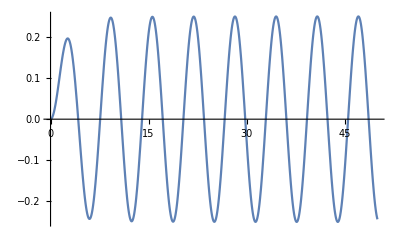
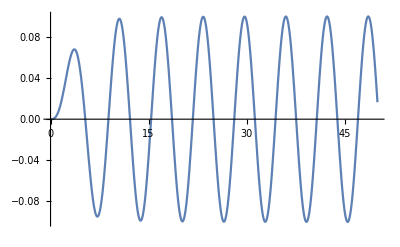
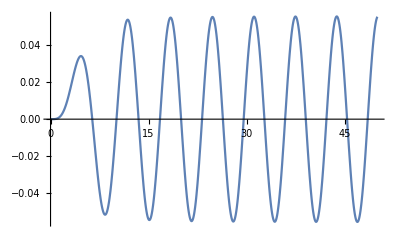
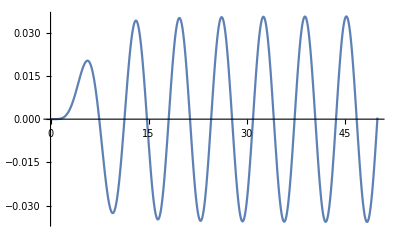
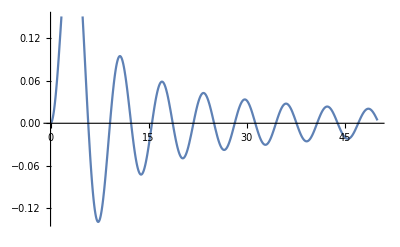
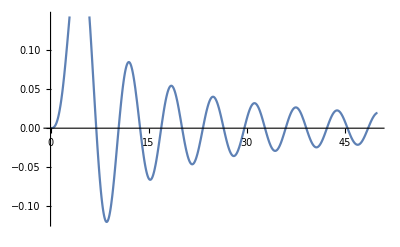
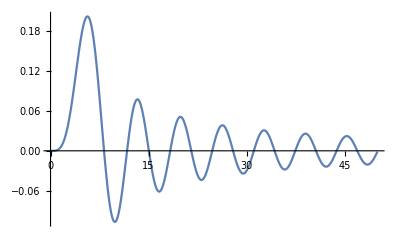
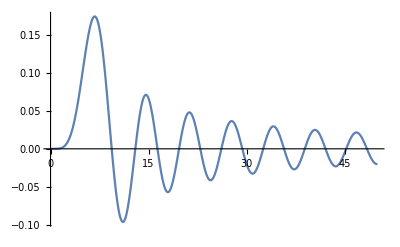
f23 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
f13 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
fe | -Graphics- | -Graphics- | -Graphics- | -Graphics-
fo | -Graphics- | -Graphics- | -Graphics- | -Graphics-
f12 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{
{"f23"}~Join~Table[plt[radial][sln[Generic][f[23]]/.{C[1]->1,C[2]->0,ω->1},{0,50}],{l,2,5}],
{"f13"}~Join~Table[plt[radial][sln[Generic][f[13]]/.{C[1]->1,C[2]->0,ω->1},{0,50}],{l,2,5}],
{"fe"}~Join~Table[plt[radial][sln[Generic][f[Even]]/.{C[3]->1,C[4]->0,ω->1},{0,50}],{l,2,5}],
{"fo"}~Join~Table[plt[radial][sln[Generic][f[Odd]]/.{C[3]->1,C[4]->0,ω->1},{0,50}],{l,2,5}],
{"f12"}~Join~Table[plt[radial][sln[Generic][f[12]]/.{C[3]->1,C[4]->0,ω->1},{0,50}],{l,2,5}]
},Frame->All]
```

### Плотность и поток энергии

```mathematica
intern[Generic][Odd][series][3];
```

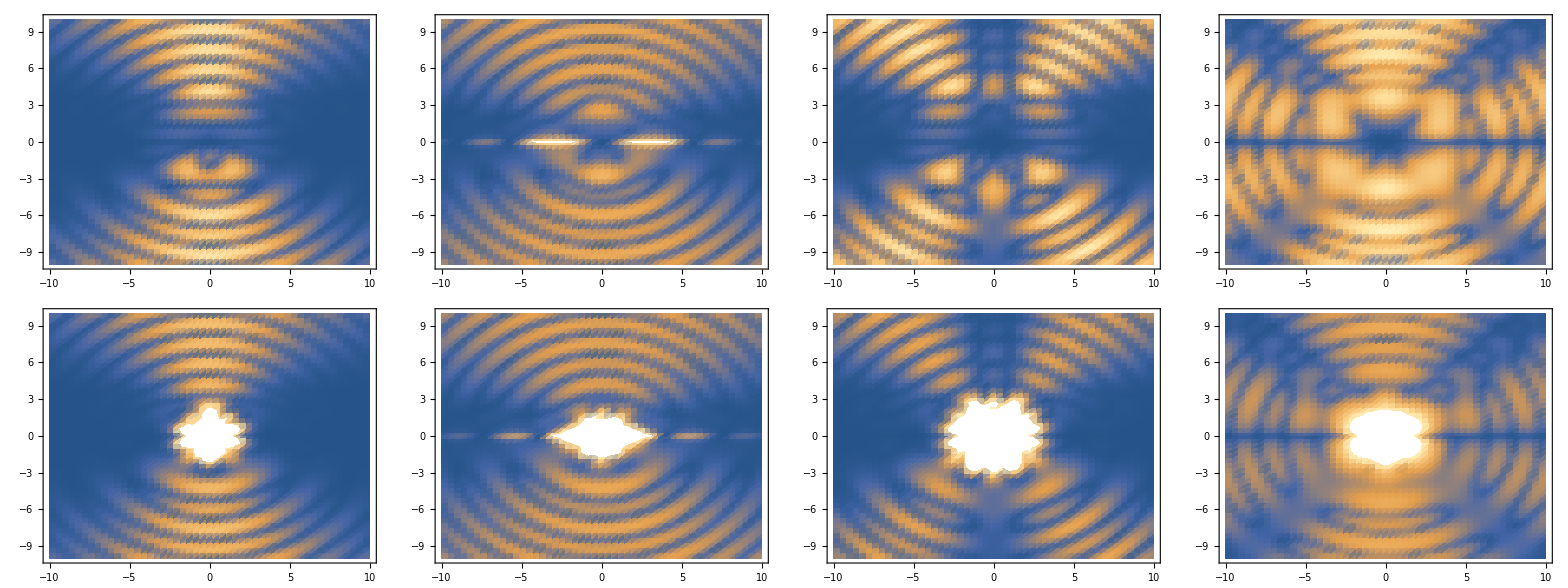

```mathematica
Table[denplt[energy][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(cache[Generic][Odd][series,energy][[Sequence@@#]]/.c&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize,{c,{{C[1]->1,C[2]->0},{C[1]->0,C[2]->1}}}]//Grid
```

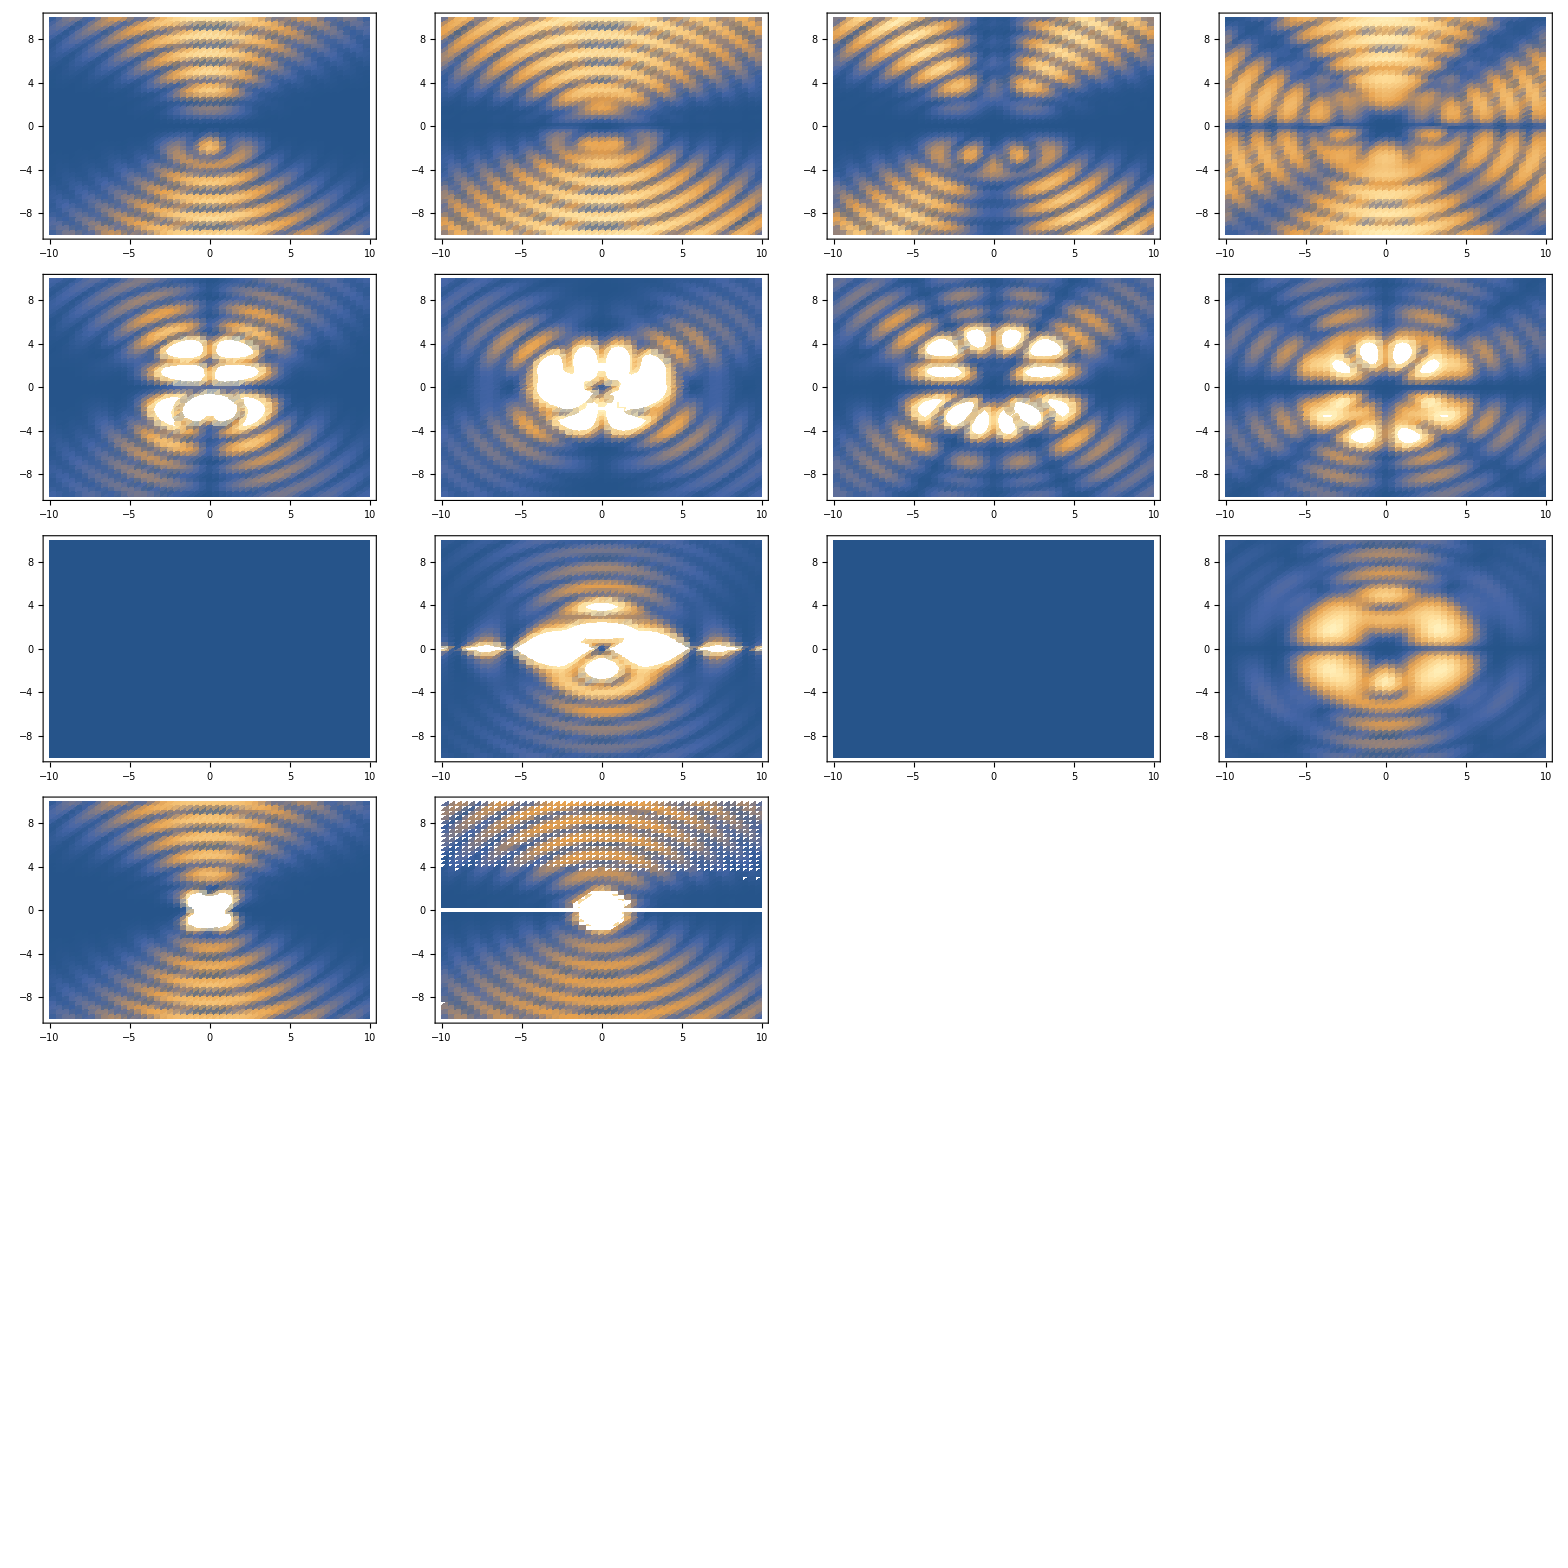

```mathematica
Table[denplt[pointing,{1,2,3}][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(cache[Generic][Odd][series,pointing][[Sequence@@#]]/.c&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose,{c,{{C[1]->1,C[2]->0},{C[1]->0,C[2]->1}}}]//Flatten[#,1]&//Grid
```

```mathematica
intern[Generic][Even][series][3];
```

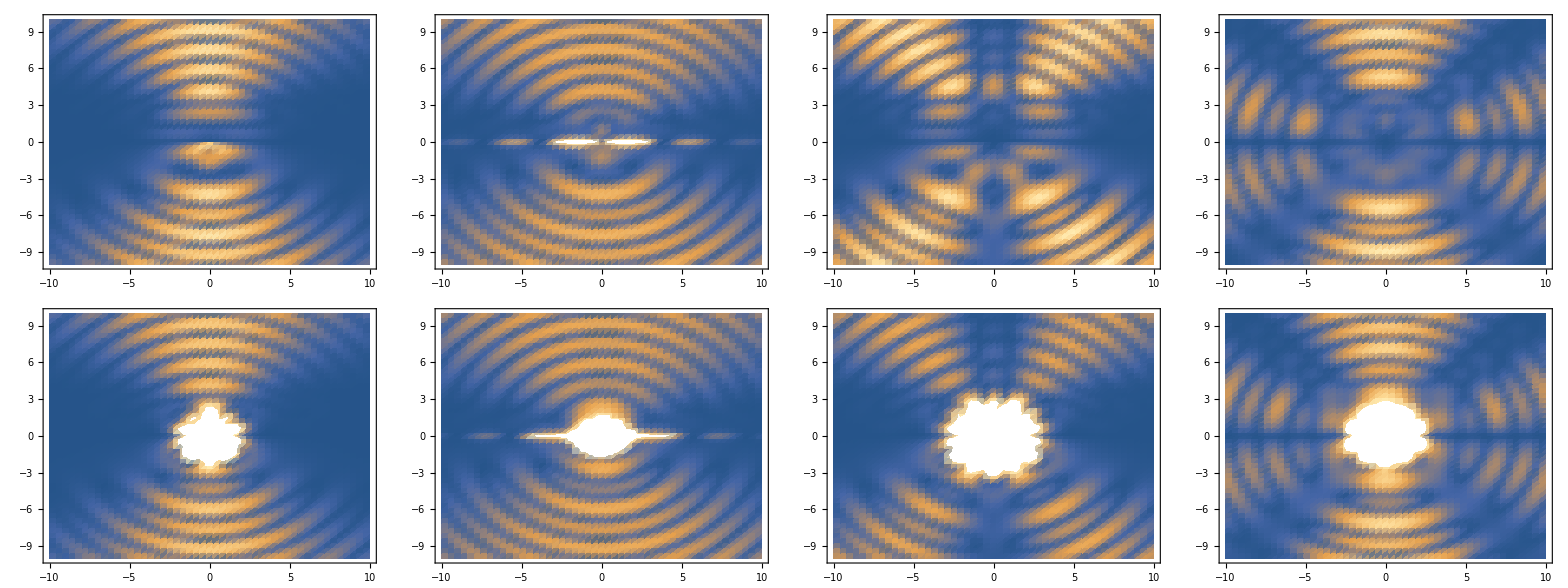

```mathematica
Table[denplt[energy][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(cache[Generic][Even][series,energy][[Sequence@@#]]/.c&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize,{c,{{C[3]->1,C[4]->0},{C[3]->0,C[4]->1}}}]//Grid
```

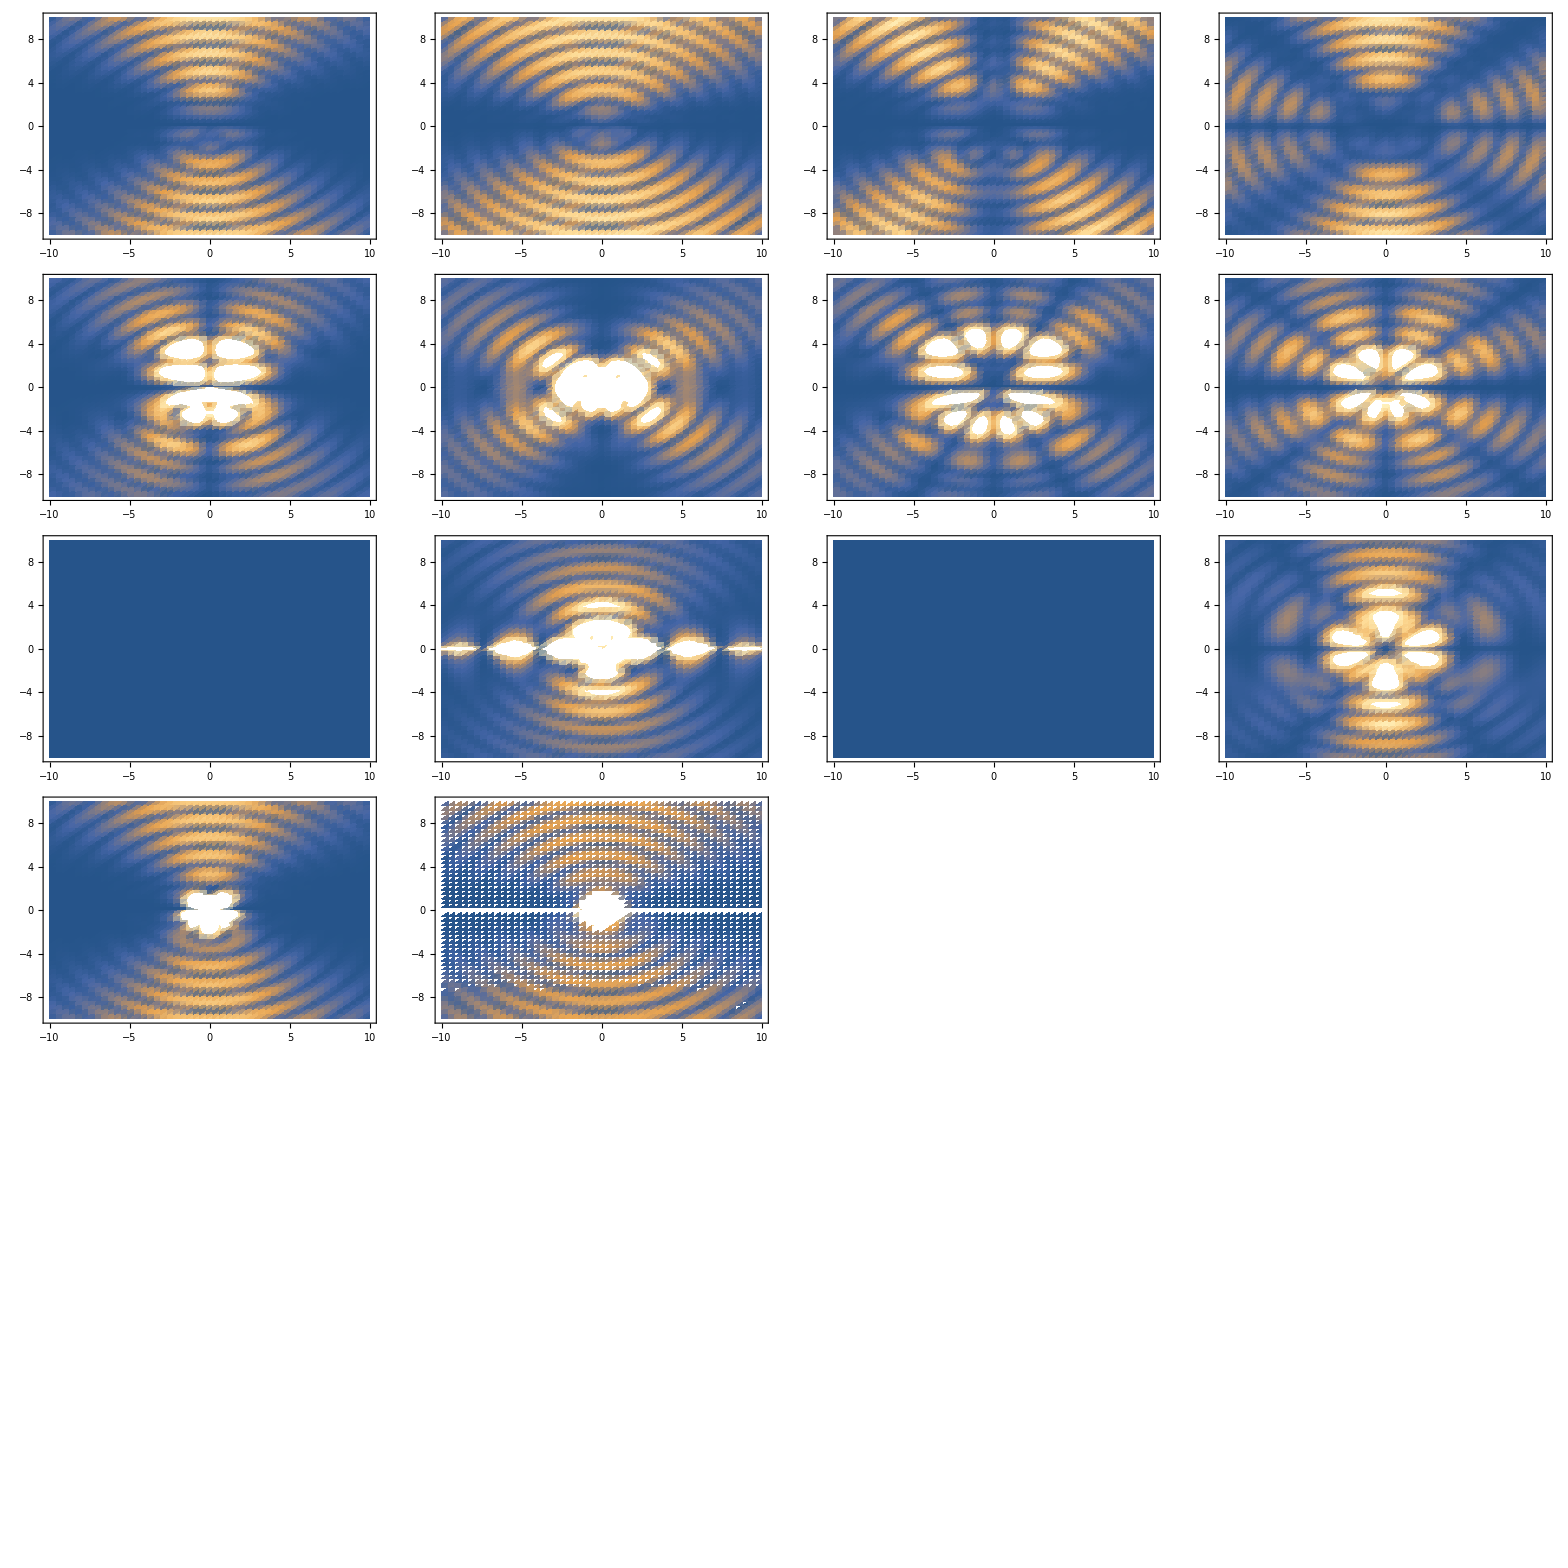

```mathematica
Table[denplt[pointing,{1,2,3}][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(cache[Generic][Even][series,pointing][[Sequence@@#]]/.c&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose,{c,{{C[3]->1,C[4]->0},{C[3]->0,C[4]->1}}}]//Flatten[#,1]&//Grid
```

### Различные соотношения

```mathematica
intern[Generic][Odd][series][5,{}]
```

```mathematica
eq[sdivh][cache[Generic][Odd][series,Tensor][[Sequence@@#]]]&/@{{1,1},{2,1},{3,1},{4,1}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],ω->1,ct->0}//Simplify
```

{{{0,0,0.+3.03577×10^-18 C[1]},{0,0,0.-1.21431×10^-17 C[1]},{0,0,6.07153×10^-18 C[1]+1.11022×10^-16 C[2]},{0,0,5.20417×10^-18 C[1]+4.44089×10^-16 C[2]}},{{0,0,0.+1.73472×10^-18 C[1]},{0,0,-1.01915×10^-17 C[1]+6.93889×10^-18 C[2]},{0,0,1.56125×10^-17 C[1]+2.77556×10^-17 C[2]},{0,0,-5.20417×10^-18 C[1]+5.55112×10^-17 C[2]}},{{0,0,0.+1.73472×10^-18 C[1]+1.73472×10^-18 C[2]},{0,0,-1.12757×10^-17 C[1]-6.93889×10^-18 C[2]},{0,0,8.67362×10^-19 C[1]+6.93889×10^-18 C[2]},{0,0,0.-1.73472×10^-18 C[1]}},{{0,0,0.-5.20417×10^-18 C[1]+4.33681×10^-19 C[2]},{0,0,-1.56125×10^-17 C[1]-3.46945×10^-18 C[2]},{0,0,-3.68629×10^-18 C[1]-6.93889×10^-18 C[2]},{0,0,1.38778×10^-17 C[1]+1.38778×10^-17 C[2]}}}

```mathematica
eq[sdivh][cache[Generic][Odd][series,Tensor][[Sequence@@#]]]&/@{{1,2},{2,3}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],w->RandomReal[{0,2π}],ω->1,ct->0}//Simplify
```

{{{(0.108072-0.058646 ⅈ) C[1]-(0.0966372-0.0524406 ⅈ) C[2],(0.+0. ⅈ)+(0.130973-0.071073 ⅈ) C[1]+(0.0808681-0.0438834 ⅈ) C[2],(-0.238672-0.439823 ⅈ) C[1]-(0.147366+0.271565 ⅈ) C[2]},{(0.+0. ⅈ)+(0.112364+0.529843 ⅈ) C[1]-(0.375421+1.77027 ⅈ) C[2],(0.0781397+0.368462 ⅈ) C[1]+(0.0283785+0.133817 ⅈ) C[2],(2.74144-0.581376 ⅈ) C[1]+(0.995625-0.211142 ⅈ) C[2]}},{{(0.0728417-0.0395278 ⅈ) C[1]-(0.0177992-0.0096588 ⅈ) C[2],(0.+0. ⅈ)+(0.0630461-0.0342122 ⅈ) C[1]+(0.117188-0.0635926 ⅈ) C[2],(-0.114889-0.211717 ⅈ) C[1]-(0.213552+0.393532 ⅈ) C[2]},{(0.+0. ⅈ)+(0.103739+0.489173 ⅈ) C[1]-(0.149065+0.702903 ⅈ) C[2],(0.073444+0.34632 ⅈ) C[1]+(0.0359884+0.169701 ⅈ) C[2],(2.57669-0.546439 ⅈ) C[1]+(1.26261-0.267762 ⅈ) C[2]}},{{(0.0420552-0.0228215 ⅈ) C[1]+(0.0129573-0.00703132 ⅈ) C[2],(0.+0. ⅈ)-(0.00892639-0.00484394 ⅈ) C[1]+(0.115573-0.0627164 ⅈ) C[2],(0.0162666+0.0299759 ⅈ) C[1]-(0.21061+0.38811 ⅈ) C[2]},{(0.+0. ⅈ)+(0.0854955+0.403147 ⅈ) C[1]-(0.0529031+0.249461 ⅈ) C[2],(0.0514585+0.242649 ⅈ) C[1]+(0.0566315+0.267041 ⅈ) C[2],(1.80536-0.382862 ⅈ) C[1]+(1.98685-0.42135 ⅈ) C[2]}},{{(0.0181551-0.00985193 ⅈ) C[1]+(0.0214503-0.0116401 ⅈ) C[2],(0.+0. ⅈ)-(0.063719-0.0345774 ⅈ) C[1]+(0.0799226-0.0433704 ⅈ) C[2],(0.116115+0.213976 ⅈ) C[1]-(0.145643+0.26839 ⅈ) C[2]},{(0.+0. ⅈ)+(0.0618904+0.29184 ⅈ) C[1]-(0.00509599+0.0240297 ⅈ) C[2],(0.0180463+0.0850959 ⅈ) C[1]+(0.0677209+0.319333 ⅈ) C[2],(0.633131-0.134268 ⅈ) C[1]+(2.3759-0.503858 ⅈ) C[2]}}}

```mathematica
intern[Generic][Even][series][5,{}]
```

```mathematica
eq[sdivh][cache[Generic][Even][series,Tensor][[Sequence@@#]]]&/@{{1,1},{2,1},{3,1},{4,1}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],ω->1,ct->0}//Simplify
```

{{{0.+4.16334×10^-17 C[3],-1.38778×10^-17 C[3]-3.46945×10^-18 C[4],0},{1.19262×10^-17 C[3]-2.77556×10^-17 C[4],8.67362×10^-18 C[3]+9.71445×10^-17 C[4],0},{1.30104×10^-18 C[3]+1.11022×10^-16 C[4],6.93889×10^-18 C[3]+2.22045×10^-16 C[4],0},{-7.58942×10^-19 C[3]+1.66533×10^-16 C[4],-1.64799×10^-17 C[3]+4.44089×10^-16 C[4],0}},{{1.38778×10^-17 C[3]-6.93889×10^-18 C[4],0.-6.93889×10^-18 C[3],0},{8.67362×10^-18 C[3]-1.38778×10^-17 C[4],-1.04083×10^-17 C[3]+3.1225×10^-17 C[4],0},{5.85469×10^-18 C[3]+4.85723×10^-17 C[4],1.01915×10^-17 C[3]-4.16334×10^-17 C[4],0},{2.27682×10^-18 C[3]+4.16334×10^-17 C[4],-1.43115×10^-17 C[3]+3.88578×10^-16 C[4],0}},{{1.04083×10^-17 C[3]+5.20417×10^-18 C[4],0.+6.93889×10^-18 C[3],0},{1.04083×10^-17 C[3]-6.93889×10^-18 C[4],-7.28584×10^-17 C[3]+5.37764×10^-17 C[4],0},{-5.42101×10^-19 C[3]+2.25514×10^-17 C[4],0.+4.16334×10^-17 C[4],0},{3.41524×10^-18 C[3]+6.93889×10^-18 C[4],2.60209×10^-18 C[3]+1.38778×10^-17 C[4],0}},{{3.46945×10^-18 C[3]+5.63785×10^-18 C[4],-1.38778×10^-17 C[3]-6.93889×10^-18 C[4],0},{0.+3.46945×10^-18 C[3],-4.51028×10^-17 C[3]+2.42861×10^-17 C[4],0},{3.79471×10^-19 C[3]+3.46945×10^-18 C[4],-1.73472×10^-18 C[3]+4.77049×10^-18 C[4],0},{-4.33681×10^-19 C[3]+3.46945×10^-18 C[4],-2.1684×10^-18 C[3]-2.08167×10^-17 C[4],0}}}

```mathematica
eq[sdivh][cache[Generic][Even][series,Tensor][[Sequence@@#]]]&/@{{1,2},{2,3}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],w->RandomReal[{0,2π}],ω->1,ct->0}//Simplify
```

{{{(0.0102631-0.0287073 ⅈ) C[3]+(0.0168724-0.0471944 ⅈ) C[4],(0.0680402+0.0334066 ⅈ) C[3]-(0.146882+0.0129182 ⅈ) C[4],(-0.0132297+0.070812 ⅈ) C[3]+(0.00540636-0.0959192 ⅈ) C[4]},{(0.100899+0.0671348 ⅈ) C[3]+(0.165877+0.110369 ⅈ) C[4],(-0.0432657-0.098631 ⅈ) C[3]+(0.335462-0.126695 ⅈ) C[4],(-0.0666933-0.161708 ⅈ) C[3]+(0.286247+0.566823 ⅈ) C[4]}},{{(0.00172281-0.00481894 ⅈ) C[3]+(0.0113003-0.0316086 ⅈ) C[4],(0.129968+0.00594361 ⅈ) C[3]-(0.0789907-0.00785439 ⅈ) C[4],(-0.00263774+0.0795954 ⅈ) C[3]-(0.00288167+0.0373453 ⅈ) C[4]},{(0.0593466+0.0394871 ⅈ) C[3]+(0.0799536+0.0531983 ⅈ) C[4],(-0.101556+0.0561795 ⅈ) C[3]+(0.222435-0.263566 ⅈ) C[4],(-0.0820405-0.15786 ⅈ) C[3]+(0.143301+0.237467 ⅈ) C[4]}},{{(-0.00244985+0.00685255 ⅈ) C[3]+(0.00675313-0.0188894 ⅈ) C[4],(0.137878-0.00895076 ⅈ) C[3]+(0.00677067+0.00427855 ⅈ) C[4],(0.00316861+0.0697644 ⅈ) C[3]-(0.00168972-0.00796445 ⅈ) C[4]},{(0.0246898+0.0164277 ⅈ) C[3]+(0.0588656+0.0391671 ⅈ) C[4],(-0.145912+0.194984 ⅈ) C[3]+(0.13081-0.217494 ⅈ) C[4],(-0.0882803-0.138747 ⅈ) C[3]+(0.0680873+0.0914866 ⅈ) C[4]}},{{(-0.00374779+0.0104831 ⅈ) C[3]+(0.00298283-0.00834337 ⅈ) C[4],(0.0987772-0.011599 ⅈ) C[3]+(0.0760725-0.00569784 ⅈ) C[4],(0.00429857+0.0449905 ⅈ) C[3]+(0.00204524+0.0377611 ⅈ) C[4]},{(-0.000195531-0.0001301 ⅈ) C[3]+(0.0436594+0.0290494 ⅈ) C[4],(-0.160283+0.271771 ⅈ) C[3]+(0.0406944-0.08809 ⅈ) C[4],(-0.0820629-0.108037 ⅈ) C[3]+(0.0158911+0.0127177 ⅈ) C[4]}}}